```mathematica
mm=Log[20 √5];
ss=√Log[5/4];
{mm,ss}
```

{Log[20 √5],√Log[5/4]}

```mathematica
With[{d=LogNormalDistribution[mm,ss]},
{Mean[d],StandardDeviation[d]}]
```

{50,25}

```mathematica
testSet1={#,(1+1/10 LegendreP[2,#])RandomVariate[LogNormalDistribution[mm,ss]]}&/@RandomReal[{-1,1},10000]
```

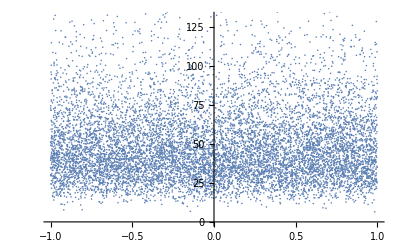

```mathematica
testSet1a={#,(1+1/10 LegendreP[10,#])RandomVariate[LogNormalDistribution[mm,ss]]}&/@RandomReal[{-1,1},10000];ListPlot[testSet1a]
```

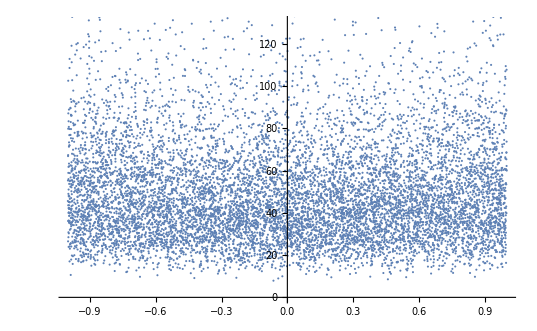

```mathematica
ListPlot[testSet1]
```

```mathematica
StandardDeviation[testSet1[[All,2]]]
```

24.9579

```mathematica
Mean[testSet1[[All,2]]]
```

49.8643

```mathematica
lmf=LinearModelFit[testSet1,{1,LegendreP[2,z],LegendreP[4,z]},z]
```

FittedModel[49.867+2.50934 (-1+3 z^2)-0.109937 (3-30 z^2+35 z^4)]

```mathematica
lmf["ParameterTable"]
```

General::munfl: Exp[-8072.69] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
1 | 49.867 | 0.248651 | 200.551 | 0.
1/2 (-1+3 z^2) | 5.01869 | 0.548993 | 9.14163 | 7.34885×10^-20
1/8 (3-30 z^2+35 z^4) | -0.879496 | 0.740608 | -1.18753 | 0.235046

```mathematica
lmf10=LinearModelFit[testSet1,{1,LegendreP[2,z],LegendreP[4,z],LegendreP[6,z],LegendreP[8,z],LegendreP[10,z]},z]
```

FittedModel[49.8683+2.51544 (-1+3 z^2)-«19» «1»-«1»+0.0016518 («1»)+0.00083571 (-63+3465 z^2-30030 z^4+90090 z^6-109395 z^8+46189 z^10)]

```mathematica
lmf10a=LinearModelFit[testSet1a,{1,LegendreP[2,z],LegendreP[4,z],LegendreP[6,z],LegendreP[8,z],LegendreP[10,z]},z]
```

FittedModel[50.2878+0.1758 (-1+3 z^2)-«21» «1»+«1»-0.00256299 («1»)+0.027404 (-63+3465 z^2-30030 z^4+90090 z^6-109395 z^8+46189 z^10)]

```mathematica
lmf10["ParameterTable"]
```

General::munfl: Exp[-8070.7] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
1 | 49.8683 | 0.248681 | 200.531 | 0.
1/2 (-1+3 z^2) | 5.03088 | 0.549213 | 9.16017 | 6.19927×10^-20
1/8 (3-30 z^2+35 z^4) | -0.871422 | 0.740941 | -1.1761 | 0.239582
1/16 (-5+105 z^2-315 z^4+231 z^6) | -0.834403 | 0.892552 | -0.934851 | 0.349888
1/128 (35-1260 z^2+6930 z^4-12012 z^6+6435 z^8) | 0.21143 | 1.00883 | 0.209579 | 0.834
1/256 (-63+3465 z^2-30030 z^4+90090 z^6-109395 z^8+46189 z^10) | 0.213942 | 1.13052 | 0.189242 | 0.849907

```mathematica
lmf10a["ParameterTable"]
```

General::munfl: Exp[-7931.4] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
1 | 50.2878 | 0.255191 | 197.06 | 0.
1/2 (-1+3 z^2) | 0.351601 | 0.567775 | 0.619261 | 0.535759
1/8 (3-30 z^2+35 z^4) | -0.391343 | 0.759511 | -0.515257 | 0.606385
1/16 (-5+105 z^2-315 z^4+231 z^6) | 0.885442 | 0.917793 | 0.96475 | 0.334693
1/128 (35-1260 z^2+6930 z^4-12012 z^6+6435 z^8) | -0.328062 | 1.05533 | -0.310861 | 0.755912
1/256 (-63+3465 z^2-30030 z^4+90090 z^6-109395 z^8+46189 z^10) | 7.01543 | 1.17227 | 5.98449 | 2.24529×10^-9

```mathematica
lmf10["CorrelationMatrix"]//MatrixForm
```

(1. | -0.00167885 | -0.0275801 | -0.00509482 | 0.00394312 | -0.00058784
-0.00167885 | 1. | -0.0220551 | -0.0233564 | -0.0027184 | 0.00732267
-0.0275801 | -0.0220551 | 1. | -0.0163695 | -0.0201121 | -0.00178961
-0.00509482 | -0.0233564 | -0.0163695 | 1. | -0.0149751 | -0.0421885
0.00394312 | -0.0027184 | -0.0201121 | -0.0149751 | 1. | -0.013831
-0.00058784 | 0.00732267 | -0.00178961 | -0.0421885 | -0.013831 | 1.)

```mathematica
lmf10["CovarianceMatrix"]//MatrixForm
```

(0.0618424 | -0.000229295 | -0.00508186 | -0.00113085 | 0.000989241 | -0.000165265
-0.000229295 | 0.301635 | -0.00897499 | -0.0114493 | -0.00150616 | 0.00454661
-0.00508186 | -0.00897499 | 0.548993 | -0.0108256 | -0.0150335 | -0.00149906
-0.00113085 | -0.0114493 | -0.0108256 | 0.796648 | -0.0134841 | -0.0425701
0.000989241 | -0.00150616 | -0.0150335 | -0.0134841 | 1.01774 | -0.0157744
-0.000165265 | 0.00454661 | -0.00149906 | -0.0425701 | -0.0157744 | 1.27807)

```mathematica
lmf["RSquared"]
```

0.00838503

```mathematica
lmf10["RSquared"]
```

0.00847785

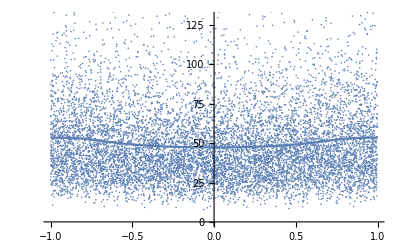

```mathematica
Show[ListPlot[testSet1],Plot[lmf10[z],{z,-1,1}]]
```

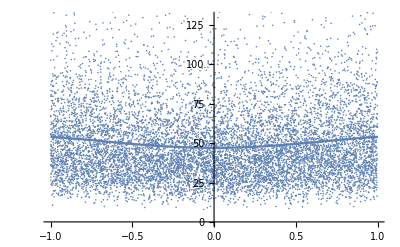

```mathematica
Show[ListPlot[testSet1],Plot[lmf[z],{z,-1,1}]]
```

```mathematica
min10=NMaximize[{lmf10[z],-1<=z<=1},z]
```

{53.6188,{z→-1.}}

```mathematica
NMaximize[{lmf[z],-1<=z<=1},z]
```

{54.0062,{z→-1.}}

```mathematica
lmf["BasisFunctions"]
```

{1,1/2 (-1+3 z^2),1/8 (3-30 z^2+35 z^4)}

```mathematica
cvec=lmf["BasisFunctions"]/.z->-1
```

{1,1,1}

```mathematica
Sqrt[cvec.lmf["CovarianceMatrix"].cvec]
```

0.939562

```mathematica
cvec10=lmf10["BasisFunctions"]/.min10[[2]]
```

{1,1.,1.,1.,1.,1.}

```mathematica
Sqrt[cvec10.lmf10["CovarianceMatrix"].cvec10]
```

1.93922